```mathematica
Lecture 13: Combinatorics
```

## Words

### Exercise Subsection

Let a[n] be the number of words of length n with letters 0 or 1 that feature at least 2 consecutive 0’s.  Create a list of the first 20 values for a[n], then look this sequence up in the OEIS (see https://oeis.org/ ).

```mathematica
a[n_]:=Count[Tuples[{0,1},n],{___,0,0,___}]
```

```mathematica
a/@Range@20//oeis
```

```mathematica
Table[2^n-Fibonacci[n+2],{n,1,20}]
```

{0,1,3,8,19,43,94,201,423,880,1815,3719,7582,15397,31171,62952,126891,255379,513342,1030865}

```mathematica
oeis[L_]:=SystemOpen@StringJoin["https://oeis.org/search?q=",StringDrop[StringDrop[ToString[L],1],-1]]
```

### Exercise Subsection

a. How many words of length 6 with letters in 1,2,3,4,5,6 (that is, consider Tuples[Range@6,6]) never have i in position i for any i?

b. Use the Monte-Carlo method to estimate the probability that a random word of length n with letters in 1,2,...,n never has i in position i for any i.

```mathematica
yawn[n_]:=Count[Tuples[Range@n,n],w_/;Not@MemberQ[w-Range@n,0]]
```

```mathematica
yawn/@Range@7
```

{0,1,8,81,1024,15625,279936}

```mathematica
test[w_]:=Not@MemberQ[w-Range@Length@w,0]
```

```mathematica
Count[Table[test@Table[RandomInteger[{1,20}],20],10^6],True]/10^6//N
```

0.359359

```mathematica
1/E//N
```

0.367879

### Exercise Subsection

What is the probability that a randomly selected Permutation of {1,2,2,3,3,3,4,4,4,4} begins with a 4?

```mathematica
Count[Permutations@{1,2,2,3,3,3,4,4,4,4},p_/;p[[1]]==4]/Length@Permutations@{1,2,2,3,3,3,4,4,4,4}//N
```

0.4

### Exercise Subsection

How many ways can the letters in the word “knickknack” be permuted such that consecutive letters are never the same?

```mathematica
Length@DeleteCases[Permutations@Characters@"knickknack",{___,a_,a_,___}]
```

4620

How many ways can {1,1,2,2,3,3,4,4,..,n,n} be permuted such that the pattern 212 never appears?

```mathematica
Table[Length@DeleteCases[Permutations@Join[Range@n,Range@n],{___,a_,___,b_,___,a_,___}/;a>b],{n,1,5}]
```

```mathematica
{1,3,15,105,945}//oeis
```

### Exercise Subsection

How many ways can 1,1,2,2,3,3,4,4,5,5 can be permuted such that i is never next to i for any i?

### Exercise Subsection

What is the probability that a random word of length 12 with letters 1,2,3,4 has its letters appearing in nondecreasing order?

### Exercise Subsection

Write a function called SameBirthdayProbability[n] which uses the Monte-Carlo method to estimate the probability that at least two numbers on a list of n random integers selected between 1 and 365 will be the same.  For which value of n is this probability 0.5?  0.75?  0.90?

```mathematica
SameBirthdayProbability[n_]:=Count[Table[Not@DuplicateFreeQ@Table[RandomInteger[{1,365}],n],10^4],True]/10^4//N
```

```mathematica
Table[SameBirthdayProbability[n],{n,1,50}]
```

{0.,0.003,0.0078,0.0165,0.0258,0.0389,0.0568,0.0739,0.0951,0.1152,0.1468,0.1667,0.1949,0.2232,0.2588,0.2859,0.3126,0.3525,0.3816,0.415,0.4391,0.4751,0.5154,0.5391,0.5678,0.6051,0.6164,0.6573,0.6855,0.7132,0.7274,0.7462,0.7795,0.8009,0.8158,0.831,0.8496,0.8658,0.8778,0.8906,0.9008,0.9153,0.9181,0.9337,0.9394,0.948,0.9516,0.963,0.9681,0.9722}

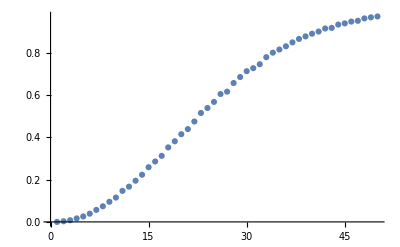

```mathematica
ListPlot@%
```

## Permutations

### Exercise Subsection

If p is a permutation of 1,2,...,n, then the permutation matrix for p is the matrix with i,j entry equal to 1 if i is equal to p[[j]] and 0 otherwise.  It is implemented in Mathematica as PermutationMatrix[p] (Mathematica stores this matrix as a “structured array” for more efficient storage and calculations, it can be turned into the standard form of a matrix using “Normal”.)

a. Write a function named FromPermutationMatrix that is the inverse function to PermutationMatrix.

b. Write a function named OrderTwo[n_] that inputs an integer n and outputs the number of permutations of 1,2,...,n that have a PermutationMatrix that is symmetric. Create a list of the first 8 values of Derangements, then look this sequence up in the OEIS (see https://oeis.org/ ).

c. Use SeriesCoefficient to create a list of the coefficient of x^n in the series centered at x = 0 for the function Exp[x + x^2/2] as n ranges from 0 to 10.  Show that multiplying the coefficient of x^n by n! gives the same result as the solution to part c.

```mathematica
FromPermutationMatrix[M_]:=First@First@Position[#,1]&/@M
```

```mathematica
FromPermutationMatrix@PermutationMatrix@{4,5,1,3,2}
```

{4,5,1,3,2}

```mathematica
OrderTwo[n_]:=Count[PermutationMatrix/@Permutations@Range@n,M_/;SymmetricMatrixQ@M]
```

```mathematica
OrderTwo/@Range@8
```

{1,2,4,10,26,76,232,764}

```mathematica
Series[Exp[x + x^2/2],{x,0,8}]
```

1+x+x^2+(2 x^3)/3+(5 x^4)/12+(13 x^5)/60+(19 x^6)/180+(29 x^7)/630+(191 x^8)/10080+O[x]^9

```mathematica
Table[n!SeriesCoefficient[Exp[x + x^2/2],{x,0,n}],{n,1,8}]
```

{1,2,4,10,26,76,232,764}

### Exercise Subsection

A permutation of 1,2,...,n is alternating if there are never three consecutive integers in the permutation a,b,c with either a<b<c or c<b<a.  

a. Write a function named Alternating[n] that inputs an integer n and outputs the number of alternating permutations of n.  Create a list of the first 8 values of Alternating, then look this sequence up in the OEIS (see https://oeis.org/ ).

b. Use Table together with SeriesCoefficient to create a list of length 8 such with nth element equal to n! times the coefficient of x^n in the series centered at x = 0 for the function (Tan[x]+Sec[x])^2.  This table should give the same values as the function Alternating.

## Lattice Paths

### Exercise Subsection

a. The Motzkin sequence of lists is defined recursively in the next cell.

```mathematica
Motzkin[n_]:=Motzkin[n]=If[n==0,{{}},
Join[Prepend[#,0]&/@Motzkin[n-1],
Flatten[Table[Flatten@{1,a,-1,b},{i,0,n-2},{a,Motzkin[i]},{b,Motzkin[n-i-2]}],2]]]
```

Starting with the empty list, the function Motzkin[n] is all of the lists that can be created by

1. adding 0 to the front of every list in Motzkin[n-1], or
2. creating a list of the form {1, a, -1, b} where a is a list in Motzkin[i] and b is a list in Motzkin[n-i-2] for some i. 

The result is that Motzkin[n] gives all lists of 0’s, 1’s and -1’s of length n such that each partial sum is nonnegative. 

a. Map the function Accumulate (this gives the partial sums of a list) onto Motzkin[8] and then verify that all lists in Motzkin[8] have nonnegative partial sums.

b. Define a function DrawPath[L_] which has input one of the lists L that is outputted by Motzkin[n] and does the following:

1. Replaces each 0 in L with {1,0}, each 1 in L with {1,1}, and each -1 in L with {1,-1}.
2. Uses Prepend to place {0,0} at the start of the list.
3. Uses Accumulate to find coordinates in the x,y plane found from the partial sums of the steps in the list.
4. Uses Graphics to draw the Line segments that pass through the coordinates.

The output of DrawPath should be a path in the plane that starts at {0,0}, ends at {n,0}, and never travels below the x-axis.

```mathematica
DrawPath[L_]:=Graphics[{Red,Line@Accumulate@Prepend[ReplaceAll[L,{0->{1,0},1->{1,1},-1->{1,-1}}],{0,0}]}]
```

c. Use DrawPath on a list in Motzkin[15] selected at random using RandomChoice.

```mathematica
DrawPath@RandomChoice@Motzkin@15
```

## Generating functions

### Exercise Subsection

The generating function for the sequence a[n] is equal to Sum[a[n] x^n, {n,0,∞}].  Find the generating functions for each of the following sequences defined in this list:

```mathematica
sequences={Binomial[n,5],Binomial[5,n],Fibonacci[n],y^n/n!,Binomial[2n,n]};
```

```mathematica
Sum[sequences[[5]]x^n,{n,0,Infinity}]
```

1/(√(1-4 x))

### Exercise Subsection

Let change[n] be the number of ways to make change for n cents using pennies, nickels, dimes, quarters, and dollar coins.  The generating function for change[n] is in the next cell.  Use Series and Coefficient to find the number of ways to make change for 100 cents.

```mathematica
Series[1/Product[(1-x^i),{i,{1,5,10,25,100}}],{x,0,1000}]
```

1+x+x^2+x^3+x^4+2 x^5+2 x^6+2 x^7+2 x^8+2 x^9+4 x^10+4 x^11+4 x^12+4 x^13+4 x^14+6 x^15+6 x^16+6 x^17+6 x^18+6 x^19+9 x^20+9 x^21+9 x^22+9 x^23+9 x^24+13 x^25+13 x^26+13 x^27+13 x^28+13 x^29+18 x^30+18 x^31+18 x^32+18 x^33+18 x^34+24 x^35+24 x^36+24 x^37+24 x^38+24 x^39+31 x^40+31 x^41+31 x^42+31 x^43+31 x^44+39 x^45+39 x^46+39 x^47+39 x^48+39 x^49+49 x^50+49 x^51+49 x^52+49 x^53+49 x^54+60 x^55+60 x^56+60 x^57+60 x^58+60 x^59+73 x^60+73 x^61+73 x^62+73 x^63+73 x^64+87 x^65+87 x^66+87 x^67+87 x^68+87 x^69+103 x^70+103 x^71+103 x^72+103 x^73+103 x^74+121 x^75+121 x^76+121 x^77+121 x^78+121 x^79+141 x^80+141 x^81+141 x^82+141 x^83+141 x^84+163 x^85+163 x^86+163 x^87+163 x^88+163 x^89+187 x^90+187 x^91+187 x^92+187 x^93+187 x^94+213 x^95+213 x^96+213 x^97+213 x^98+213 x^99+243 x^100+243 x^101+243 x^102+243 x^103+243 x^104+275 x^105+275 x^106+275 x^107+275 x^108+275 x^109+311 x^110+311 x^111+311 x^112+311 x^113+311 x^114+349 x^115+349 x^116+349 x^117+349 x^118+349 x^119+391 x^120+391 x^121+391 x^122+391 x^123+391 x^124+437 x^125+437 x^126+437 x^127+437 x^128+437 x^129+487 x^130+487 x^131+487 x^132+487 x^133+487 x^134+541 x^135+541 x^136+541 x^137+541 x^138+541 x^139+599 x^140+599 x^141+599 x^142+599 x^143+599 x^144+661 x^145+661 x^146+661 x^147+661 x^148+661 x^149+729 x^150+729 x^151+729 x^152+729 x^153+729 x^154+801 x^155+801 x^156+801 x^157+801 x^158+801 x^159+879 x^160+879 x^161+879 x^162+879 x^163+879 x^164+961 x^165+961 x^166+961 x^167+961 x^168+961 x^169+1049 x^170+1049 x^171+1049 x^172+1049 x^173+1049 x^174+1143 x^175+1143 x^176+1143 x^177+1143 x^178+1143 x^179+1243 x^180+1243 x^181+1243 x^182+1243 x^183+1243 x^184+1349 x^185+1349 x^186+1349 x^187+1349 x^188+1349 x^189+1461 x^190+1461 x^191+1461 x^192+1461 x^193+1461 x^194+1579 x^195+1579 x^196+1579 x^197+1579 x^198+1579 x^199+1706 x^200+1706 x^201+1706 x^202+1706 x^203+1706 x^204+1839 x^205+1839 x^206+1839 x^207+1839 x^208+1839 x^209+1981 x^210+1981 x^211+1981 x^212+1981 x^213+1981 x^214+2129 x^215+2129 x^216+2129 x^217+2129 x^218+2129 x^219+2286 x^220+2286 x^221+2286 x^222+2286 x^223+2286 x^224+2452 x^225+2452 x^226+2452 x^227+2452 x^228+2452 x^229+2627 x^230+2627 x^231+2627 x^232+2627 x^233+2627 x^234+2811 x^235+2811 x^236+2811 x^237+2811 x^238+2811 x^239+3004 x^240+3004 x^241+3004 x^242+3004 x^243+3004 x^244+3206 x^245+3206 x^246+3206 x^247+3206 x^248+3206 x^249+3420 x^250+3420 x^251+3420 x^252+3420 x^253+3420 x^254+3643 x^255+3643 x^256+3643 x^257+3643 x^258+3643 x^259+3878 x^260+3878 x^261+3878 x^262+3878 x^263+3878 x^264+4122 x^265+4122 x^266+4122 x^267+4122 x^268+4122 x^269+4378 x^270+4378 x^271+4378 x^272+4378 x^273+4378 x^274+4646 x^275+4646 x^276+4646 x^277+4646 x^278+4646 x^279+4926 x^280+4926 x^281+4926 x^282+4926 x^283+4926 x^284+5218 x^285+5218 x^286+5218 x^287+5218 x^288+5218 x^289+5522 x^290+5522 x^291+5522 x^292+5522 x^293+5522 x^294+5838 x^295+5838 x^296+5838 x^297+5838 x^298+5838 x^299+6170 x^300+6170 x^301+6170 x^302+6170 x^303+6170 x^304+6514 x^305+6514 x^306+6514 x^307+6514 x^308+6514 x^309+6874 x^310+6874 x^311+6874 x^312+6874 x^313+6874 x^314+7246 x^315+7246 x^316+7246 x^317+7246 x^318+7246 x^319+7634 x^320+7634 x^321+7634 x^322+7634 x^323+7634 x^324+8038 x^325+8038 x^326+8038 x^327+8038 x^328+8038 x^329+8458 x^330+8458 x^331+8458 x^332+8458 x^333+8458 x^334+8894 x^335+8894 x^336+8894 x^337+8894 x^338+8894 x^339+9346 x^340+9346 x^341+9346 x^342+9346 x^343+9346 x^344+9814 x^345+9814 x^346+9814 x^347+9814 x^348+9814 x^349+10302 x^350+10302 x^351+10302 x^352+10302 x^353+10302 x^354+10806 x^355+10806 x^356+10806 x^357+10806 x^358+10806 x^359+11330 x^360+11330 x^361+11330 x^362+11330 x^363+11330 x^364+11870 x^365+11870 x^366+11870 x^367+11870 x^368+11870 x^369+12430 x^370+12430 x^371+12430 x^372+12430 x^373+12430 x^374+13010 x^375+13010 x^376+13010 x^377+13010 x^378+13010 x^379+13610 x^380+13610 x^381+13610 x^382+13610 x^383+13610 x^384+14230 x^385+14230 x^386+14230 x^387+14230 x^388+14230 x^389+14870 x^390+14870 x^391+14870 x^392+14870 x^393+14870 x^394+15530 x^395+15530 x^396+15530 x^397+15530 x^398+15530 x^399+16215 x^400+16215 x^401+16215 x^402+16215 x^403+16215 x^404+16920 x^405+16920 x^406+16920 x^407+16920 x^408+16920 x^409+17650 x^410+17650 x^411+17650 x^412+17650 x^413+17650 x^414+18400 x^415+18400 x^416+18400 x^417+18400 x^418+18400 x^419+19175 x^420+19175 x^421+19175 x^422+19175 x^423+19175 x^424+19975 x^425+19975 x^426+19975 x^427+19975 x^428+19975 x^429+20800 x^430+20800 x^431+20800 x^432+20800 x^433+20800 x^434+21650 x^435+21650 x^436+21650 x^437+21650 x^438+21650 x^439+22525 x^440+22525 x^441+22525 x^442+22525 x^443+22525 x^444+23425 x^445+23425 x^446+23425 x^447+23425 x^448+23425 x^449+24355 x^450+24355 x^451+24355 x^452+24355 x^453+24355 x^454+25310 x^455+25310 x^456+25310 x^457+25310 x^458+25310 x^459+26295 x^460+26295 x^461+26295 x^462+26295 x^463+26295 x^464+27305 x^465+27305 x^466+27305 x^467+27305 x^468+27305 x^469+28345 x^470+28345 x^471+28345 x^472+28345 x^473+28345 x^474+29415 x^475+29415 x^476+29415 x^477+29415 x^478+29415 x^479+30515 x^480+30515 x^481+30515 x^482+30515 x^483+30515 x^484+31645 x^485+31645 x^486+31645 x^487+31645 x^488+31645 x^489+32805 x^490+32805 x^491+32805 x^492+32805 x^493+32805 x^494+33995 x^495+33995 x^496+33995 x^497+33995 x^498+33995 x^499+35221 x^500+35221 x^501+35221 x^502+35221 x^503+35221 x^504+36477 x^505+36477 x^506+36477 x^507+36477 x^508+36477 x^509+37769 x^510+37769 x^511+37769 x^512+37769 x^513+37769 x^514+39091 x^515+39091 x^516+39091 x^517+39091 x^518+39091 x^519+40449 x^520+40449 x^521+40449 x^522+40449 x^523+40449 x^524+41843 x^525+41843 x^526+41843 x^527+41843 x^528+41843 x^529+43273 x^530+43273 x^531+43273 x^532+43273 x^533+43273 x^534+44739 x^535+44739 x^536+44739 x^537+44739 x^538+44739 x^539+46241 x^540+46241 x^541+46241 x^542+46241 x^543+46241 x^544+47779 x^545+47779 x^546+47779 x^547+47779 x^548+47779 x^549+49359 x^550+49359 x^551+49359 x^552+49359 x^553+49359 x^554+50975 x^555+50975 x^556+50975 x^557+50975 x^558+50975 x^559+52633 x^560+52633 x^561+52633 x^562+52633 x^563+52633 x^564+54327 x^565+54327 x^566+54327 x^567+54327 x^568+54327 x^569+56063 x^570+56063 x^571+56063 x^572+56063 x^573+56063 x^574+57841 x^575+57841 x^576+57841 x^577+57841 x^578+57841 x^579+59661 x^580+59661 x^581+59661 x^582+59661 x^583+59661 x^584+61523 x^585+61523 x^586+61523 x^587+61523 x^588+61523 x^589+63427 x^590+63427 x^591+63427 x^592+63427 x^593+63427 x^594+65373 x^595+65373 x^596+65373 x^597+65373 x^598+65373 x^599+67368 x^600+67368 x^601+67368 x^602+67368 x^603+67368 x^604+69405 x^605+69405 x^606+69405 x^607+69405 x^608+69405 x^609+71491 x^610+71491 x^611+71491 x^612+71491 x^613+71491 x^614+73619 x^615+73619 x^616+73619 x^617+73619 x^618+73619 x^619+75796 x^620+75796 x^621+75796 x^622+75796 x^623+75796 x^624+78022 x^625+78022 x^626+78022 x^627+78022 x^628+78022 x^629+80297 x^630+80297 x^631+80297 x^632+80297 x^633+80297 x^634+82621 x^635+82621 x^636+82621 x^637+82621 x^638+82621 x^639+84994 x^640+84994 x^641+84994 x^642+84994 x^643+84994 x^644+87416 x^645+87416 x^646+87416 x^647+87416 x^648+87416 x^649+89894 x^650+89894 x^651+89894 x^652+89894 x^653+89894 x^654+92421 x^655+92421 x^656+92421 x^657+92421 x^658+92421 x^659+95004 x^660+95004 x^661+95004 x^662+95004 x^663+95004 x^664+97636 x^665+97636 x^666+97636 x^667+97636 x^668+97636 x^669+100324 x^670+100324 x^671+100324 x^672+100324 x^673+100324 x^674+103068 x^675+103068 x^676+103068 x^677+103068 x^678+103068 x^679+105868 x^680+105868 x^681+105868 x^682+105868 x^683+105868 x^684+108724 x^685+108724 x^686+108724 x^687+108724 x^688+108724 x^689+111636 x^690+111636 x^691+111636 x^692+111636 x^693+111636 x^694+114604 x^695+114604 x^696+114604 x^697+114604 x^698+114604 x^699+117636 x^700+117636 x^701+117636 x^702+117636 x^703+117636 x^704+120724 x^705+120724 x^706+120724 x^707+120724 x^708+120724 x^709+123876 x^710+123876 x^711+123876 x^712+123876 x^713+123876 x^714+127084 x^715+127084 x^716+127084 x^717+127084 x^718+127084 x^719+130356 x^720+130356 x^721+130356 x^722+130356 x^723+130356 x^724+133692 x^725+133692 x^726+133692 x^727+133692 x^728+133692 x^729+137092 x^730+137092 x^731+137092 x^732+137092 x^733+137092 x^734+140556 x^735+140556 x^736+140556 x^737+140556 x^738+140556 x^739+144084 x^740+144084 x^741+144084 x^742+144084 x^743+144084 x^744+147676 x^745+147676 x^746+147676 x^747+147676 x^748+147676 x^749+151340 x^750+151340 x^751+151340 x^752+151340 x^753+151340 x^754+155068 x^755+155068 x^756+155068 x^757+155068 x^758+155068 x^759+158868 x^760+158868 x^761+158868 x^762+158868 x^763+158868 x^764+162732 x^765+162732 x^766+162732 x^767+162732 x^768+162732 x^769+166668 x^770+166668 x^771+166668 x^772+166668 x^773+166668 x^774+170676 x^775+170676 x^776+170676 x^777+170676 x^778+170676 x^779+174756 x^780+174756 x^781+174756 x^782+174756 x^783+174756 x^784+178908 x^785+178908 x^786+178908 x^787+178908 x^788+178908 x^789+183132 x^790+183132 x^791+183132 x^792+183132 x^793+183132 x^794+187428 x^795+187428 x^796+187428 x^797+187428 x^798+187428 x^799+191805 x^800+191805 x^801+191805 x^802+191805 x^803+191805 x^804+196254 x^805+196254 x^806+196254 x^807+196254 x^808+196254 x^809+200784 x^810+200784 x^811+200784 x^812+200784 x^813+200784 x^814+205386 x^815+205386 x^816+205386 x^817+205386 x^818+205386 x^819+210069 x^820+210069 x^821+210069 x^822+210069 x^823+210069 x^824+214833 x^825+214833 x^826+214833 x^827+214833 x^828+214833 x^829+219678 x^830+219678 x^831+219678 x^832+219678 x^833+219678 x^834+224604 x^835+224604 x^836+224604 x^837+224604 x^838+224604 x^839+229611 x^840+229611 x^841+229611 x^842+229611 x^843+229611 x^844+234699 x^845+234699 x^846+234699 x^847+234699 x^848+234699 x^849+239877 x^850+239877 x^851+239877 x^852+239877 x^853+239877 x^854+245136 x^855+245136 x^856+245136 x^857+245136 x^858+245136 x^859+250485 x^860+250485 x^861+250485 x^862+250485 x^863+250485 x^864+255915 x^865+255915 x^866+255915 x^867+255915 x^868+255915 x^869+261435 x^870+261435 x^871+261435 x^872+261435 x^873+261435 x^874+267045 x^875+267045 x^876+267045 x^877+267045 x^878+267045 x^879+272745 x^880+272745 x^881+272745 x^882+272745 x^883+272745 x^884+278535 x^885+278535 x^886+278535 x^887+278535 x^888+278535 x^889+284415 x^890+284415 x^891+284415 x^892+284415 x^893+284415 x^894+290385 x^895+290385 x^896+290385 x^897+290385 x^898+290385 x^899+296455 x^900+296455 x^901+296455 x^902+296455 x^903+296455 x^904+302615 x^905+302615 x^906+302615 x^907+302615 x^908+302615 x^909+308875 x^910+308875 x^911+308875 x^912+308875 x^913+308875 x^914+315225 x^915+315225 x^916+315225 x^917+315225 x^918+315225 x^919+321675 x^920+321675 x^921+321675 x^922+321675 x^923+321675 x^924+328225 x^925+328225 x^926+328225 x^927+328225 x^928+328225 x^929+334875 x^930+334875 x^931+334875 x^932+334875 x^933+334875 x^934+341625 x^935+341625 x^936+341625 x^937+341625 x^938+341625 x^939+348475 x^940+348475 x^941+348475 x^942+348475 x^943+348475 x^944+355425 x^945+355425 x^946+355425 x^947+355425 x^948+355425 x^949+362485 x^950+362485 x^951+362485 x^952+362485 x^953+362485 x^954+369645 x^955+369645 x^956+369645 x^957+369645 x^958+369645 x^959+376915 x^960+376915 x^961+376915 x^962+376915 x^963+376915 x^964+384285 x^965+384285 x^966+384285 x^967+384285 x^968+384285 x^969+391765 x^970+391765 x^971+391765 x^972+391765 x^973+391765 x^974+399355 x^975+399355 x^976+399355 x^977+399355 x^978+399355 x^979+407055 x^980+407055 x^981+407055 x^982+407055 x^983+407055 x^984+414865 x^985+414865 x^986+414865 x^987+414865 x^988+414865 x^989+422785 x^990+422785 x^991+422785 x^992+422785 x^993+422785 x^994+430815 x^995+430815 x^996+430815 x^997+430815 x^998+430815 x^999+438966 x^1000+O[x]^1001

### Exercise Subsection

The generating function for the Legendre polynomial is in the next cell.  Use Series and Coefficient to find the 10th Legendre polynomial.

```mathematica
1/(√(1-2 t x+x^2))
```

```mathematica
Series[1/(√(1-2 t x+x^2)),{x,0,10}]//Simplify
```

1+t x+1/2 (-1+3 t^2) x^2+1/2 t (-3+5 t^2) x^3+1/8 (3-30 t^2+35 t^4) x^4+1/8 t (15-70 t^2+63 t^4) x^5+1/16 (-5+105 t^2-315 t^4+231 t^6) x^6+1/16 t (-35+315 t^2-693 t^4+429 t^6) x^7+1/128 (35-1260 t^2+6930 t^4-12012 t^6+6435 t^8) x^8+1/128 t (315-4620 t^2+18018 t^4-25740 t^6+12155 t^8) x^9+1/256 (-63+3465 t^2-30030 t^4+90090 t^6-109395 t^8+46189 t^10) x^10+O[x]^11